# Convergencia de distribuciones bajo mapeos

Se quiere mostrar que las distribuciones de equilibrio son estables y atraen a otras distribuciones, es decir, que bajo el mapeo , las variables aleatorias  convergen en distribución a . Primero definimos una distribución de prueba con soporte en . Una opción podría ser la distribución triangular. La densidad la definimos debajo:

```mathematica
sqdens[x_]:=HeavisideTheta[x]*HeavisideTheta[1-x]*Piecewise[{{4*x,x<1/2},{4*(1-x),x>=1/2}}];
```

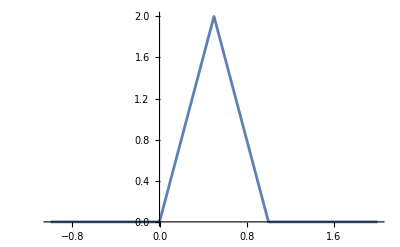

```mathematica
Plot[sqdens[x],{x,-1,2}]
```

## Ecuación logística

Primero consideramos la ecuación logística con . Suponemos que tenemos una variable aleatoria  con densidad . Definimos ahora a . Usando la función distribución acumulada de , , y derivando, obtenemos que su densidad está dada por

Definimos esta densidad como una función que requiere de una función (la densidad de ), y , el valor a evaluar la densidad. Iteramos varias veces y vemos que rápidamente converge a la densidad de la Beta con parámetros :

```mathematica
logdens[f_,y_]:=(1/(4*Sqrt[1-y]))*(f[(1-Sqrt[1-y])/2]+f[(1+Sqrt[1-y])/2]);
```

```mathematica
dens1[y_]:=logdens[sqdens,y];
```

```mathematica
dens2[y_]:=logdens[dens1,y];
```

```mathematica
dens3[y_]:=logdens[dens2,y];
```

```mathematica
dens4[y_]:=logdens[dens3,y];
```

```mathematica
dens5[y_]:=logdens[dens4,y];
```

```mathematica
Show[{Plot[{sqdens[y],dens1[y],dens2[y],dens3[y],dens4[y],dens5[y]},{y,0,1},AxesLabel->{y,Subscript[f,Y][y]},PlotLegends->{"Densidad original","Primer iterado","Segundo iterado","Tercer iterado","Cuarto iterado","Quinto iterado"}],Plot[PDF[BetaDistribution[1/2,1/2],y],{y,0,1},PlotStyle->{Black,Dashed,Thick}]}]
```

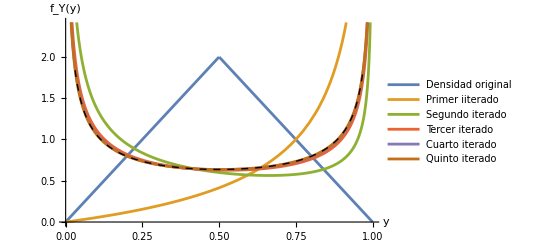

## Tent map

Ahora definimos la función , la cual es igual a , cuando , e igual a  cuando . De igual manera, si  tiene densidad , y , entonces  tiene densidad 

Usamos ahora una densidad beta inicial, y vemos como la densidad va convergiendo a la densidad uniforme.

```mathematica
betaori[y_]:=PDF[BetaDistribution[2,2],y];
```

```mathematica
tentdens[f_,y_]:=(f[y/2]+f[1-y/2])/2;
```

```mathematica
tdens1[y_]:=tentdens[betaori,y];
```

```mathematica
tdens2[y_]:=tentdens[tdens1,y];
```

```mathematica
tdens3[y_]:=tentdens[tdens2,y];
```

```mathematica
tdens4[y_]:=tentdens[tdens3,y];
```

```mathematica
tdens5[y_]:=tentdens[tdens4,y];
```

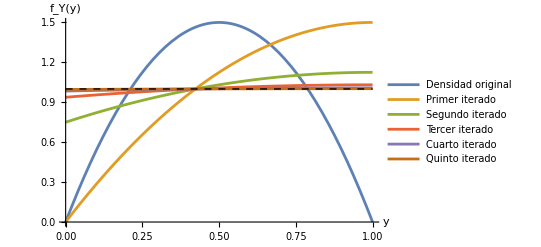

```mathematica
Show[{Plot[{betaori[y],tdens1[y],tdens2[y],tdens3[y],tdens4[y],tdens5[y]},{y,0,1},AxesLabel->{y,Subscript[f,Y][y]},PlotLegends->{"Densidad original","Primer iterado","Segundo iterado","Tercer iterado","Cuarto iterado","Quinto iterado"},PlotRange->All],Plot[PDF[UniformDistribution[{0,1}],y],{y,0,1},PlotStyle->{Black,Dashed,Thick}]}]
```